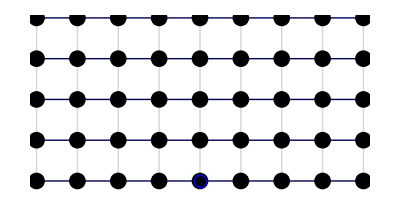
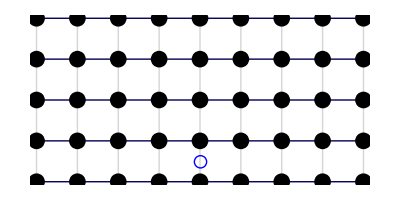
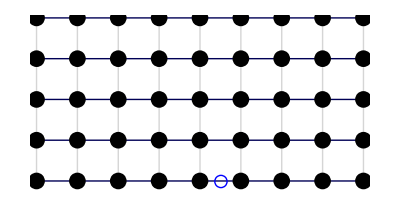
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

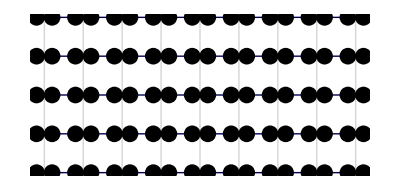
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

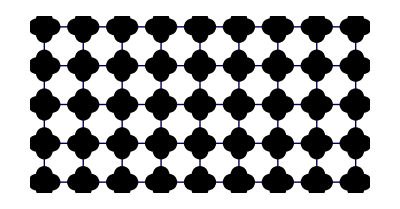
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GetPhasor[r_]:=Abs[r[[1]]+ⅈ r[[2]]]Exp[ⅈ Arg[r[[1]]+ⅈ r[[2]]]]
WC[r_,W_]:={Re[(GetPhasor[r])^W],Im[(GetPhasor[r])^W]}(*wind coordinate*)

GetAngle[r_]:=Arg[r[[1]]+ⅈ r[[2]]]
WA[ϕ_,W_]:=ϕ W(*wind angle*)
Rot[r_,ϕ_]:={{Cos[ϕ],Sin[ϕ]},{-Sin[ϕ],Cos[ϕ]}}.r;(*rotate coordinate*)

MyPoints[r_,θ_,Np_,MyPointSize_,x_]:={
White,Disk[r,x ],
Red,PointSize[1.5 MyPointSize],
Table[Point[r+ x { Cos[(2π)/Np i+θ], Sin[(2π)/Np i+θ]}],{i,0,Np-1}]
};


r1={0,1};
r2={1,0};

ColorLines=Blend[{Blue,Black,Black}];
ColorLinesWeak=Blend[{Black,White,White,White,White,White}];
ColorO1=Blue;
ColorO2=Cyan;
ColorK1=Purple;
ColorK2=Magenta;

MyFaceSx[ npoints_,MyPointSize_,ϕ_,W_,rP_]:={
ColorLinesWeak,
Line[Flatten[Table[Table[{Rot[WC[i r1+j r2-rP,W],ϕ],Rot[WC[(i-1) r1+j r2-rP,W],ϕ]},{i,1,npoints-1}],{j,-(npoints-1),npoints-1}],1]],
ColorLines,
Line[Flatten[Table[Table[{Rot[WC[i r1+j r2-rP,W],ϕ],Rot[WC[i r1+(j-1) r2-rP,W],ϕ]},{i,0,npoints-1}],{j,1-(npoints-1),npoints-1}],1]],
Black,
PointSize[MyPointSize],
Flatten[Table[Table[Point[Rot[WC[i r1+j r2-rP,W],ϕ]],{i,0,npoints-1}],{j,-(npoints-1),npoints-1}],2],
Blue,Circle[{0,0},.15]
};

MyFaceSxtbm[ npoints_,MyPointSize_,x_,ϕ_,W_,rP_]:={
ColorLinesWeak,
Line[Flatten[Table[Table[{Rot[WC[i r1+j r2-rP,W],ϕ],Rot[WC[(i-1) r1+j r2-rP,W],ϕ]},{i,1,npoints-1}],{j,-(npoints-1),npoints-1}],1]],
ColorLines,
Line[Flatten[Table[Table[{Rot[WC[i r1+j r2-x r2-rP,W],ϕ],Rot[WC[i r1+(j-1) r2+x r2-rP,W],ϕ]},{i,0,npoints-1}],{j,1-(npoints-1),npoints-1}],1]],
Black,
PointSize[MyPointSize],
(*Flatten[Table[Table[Point[Rot[WC[i r1+x r1+j r2,W],ϕ]],{i,0,npoints-1}],{j,0,npoints-1}],2],
Flatten[Table[Table[Point[Rot[WC[i r1-x r1+j r2,W],ϕ]],{i,0,npoints-1}],{j,0,npoints-1}],2],*)
Flatten[Table[Table[Point[Rot[WC[i r1+j r2+x r2-rP,W],ϕ]],{i,0,npoints-1}],{j,-(npoints-1),npoints-1}],2],
Flatten[Table[Table[Point[Rot[WC[i r1+j r2-x r2-rP,W],ϕ]],{i,0,npoints-1}],{j,-(npoints-1),npoints-1}],2](*,
Blue,Circle[{0,0},.15]*)
};
MyFaceSxytbm[ npoints_,MyPointSize_,x_,ϕ_,W_,rP_]:={
ColorLines,
Line[Flatten[Table[Table[{Rot[WC[i r1+j r2-x r1-rP,W],ϕ],Rot[WC[(i-1) r1+j r2+x r1-rP,W],ϕ]},{i,1,npoints-1}],{j,-(npoints-1),npoints-1}],1]],
ColorLines,
Line[Flatten[Table[Table[{Rot[WC[i r1+j r2-x r2-rP,W],ϕ],Rot[WC[i r1+(j-1) r2+x r2-rP,W],ϕ]},{i,0,npoints-1}],{j,1-(npoints-1),npoints-1}],1]],
Black,
PointSize[MyPointSize],
Flatten[Table[Table[Point[Rot[WC[i r1+x r1+j r2-rP,W],ϕ]],{i,0,npoints-1}],{j,-(npoints-1),npoints-1}],2],
Flatten[Table[Table[Point[Rot[WC[i r1-x r1+j r2-rP,W],ϕ]],{i,0,npoints-1}],{j,-(npoints-1),npoints-1}],2],
Flatten[Table[Table[Point[Rot[WC[i r1+j r2+x r2-rP,W],ϕ]],{i,0,npoints-1}],{j,-(npoints-1),npoints-1}],2],
Flatten[Table[Table[Point[Rot[WC[i r1+j r2-x r2-rP,W],ϕ]],{i,0,npoints-1}],{j,-(npoints-1),npoints-1}],2](*,
Blue,Circle[{0,0},.15]*)
};

npoints=5;
MyPointSize=0.03;
x=0.2;
ϕ=0;
W=3/3;
r={0,0};

{
Graphics[MyFaceSx[ npoints,MyPointSize,ϕ,W,{0,0}]],
Graphics[MyFaceSx[ npoints,MyPointSize,ϕ,W,{1/2,1/2}]],
Graphics[MyFaceSx[ npoints,MyPointSize,ϕ,W,{0,1/2}]],
Graphics[MyFaceSx[ npoints,MyPointSize,ϕ,W,{1/2,0}]]
}
{
Graphics[MyFaceSxtbm[ npoints,MyPointSize,x,ϕ,W,{0,0}]],
Graphics[MyFaceSxtbm[ npoints,MyPointSize,x,ϕ,W,{1/2,1/2}]],
Graphics[MyFaceSxtbm[ npoints,MyPointSize,x,ϕ,W,{0,1/2}]],
Graphics[MyFaceSxtbm[ npoints,MyPointSize,x,ϕ,W,{1/2,0}]]
}
{
Graphics[MyFaceSxytbm[ npoints,MyPointSize,x,ϕ,W,{0,0}]],
Graphics[MyFaceSxytbm[ npoints,MyPointSize,x,ϕ,W,{1/2,1/2}]],
Graphics[MyFaceSxytbm[ npoints,MyPointSize,x,ϕ,W,{0,1/2}]],
Graphics[MyFaceSxytbm[ npoints,MyPointSize,x,ϕ,W,{1/2,0}]]
}
```

## C_2 disclinations

{0,0}

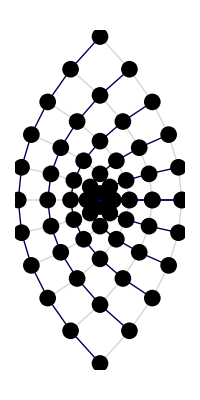
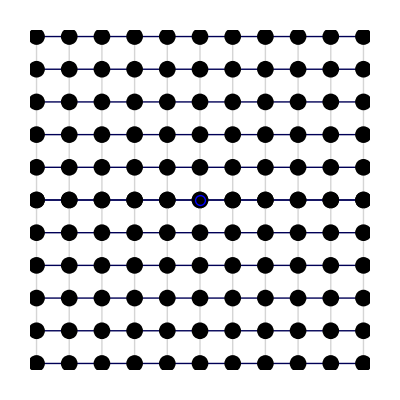
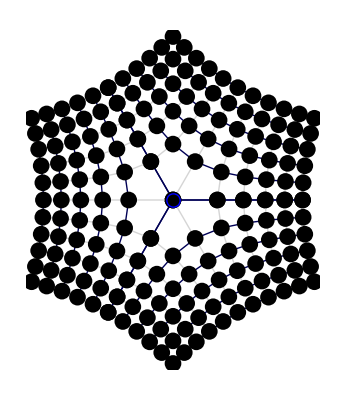

```mathematica
npoints=6;
MyPointSize=0.03;
ϕ=0;
rP={0,0}
W1=4/2;
W2=4/4;
W3=4/6;
Nq1=1;
Nq2=2;
Nq3=3;
{
Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq1)),W1,rP],{nq,1,Nq1}]],
Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq2)),W2,rP],{nq,1,Nq2}]],
Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq3)),W3,rP],{nq,1,Nq3}]]
}
```

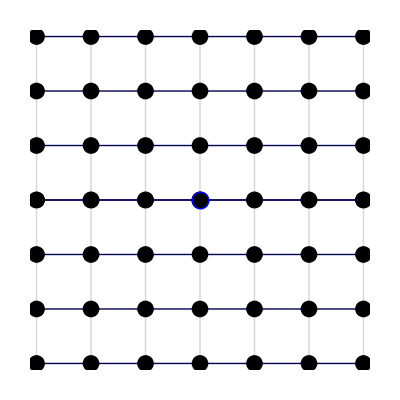
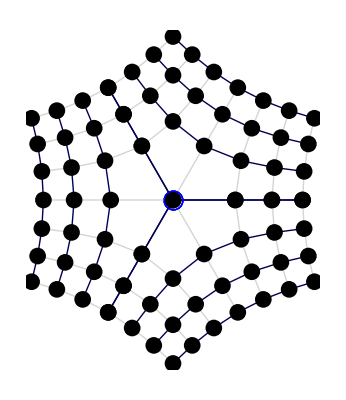
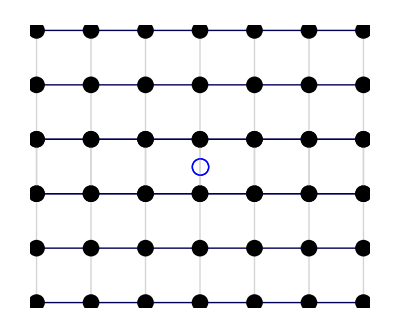
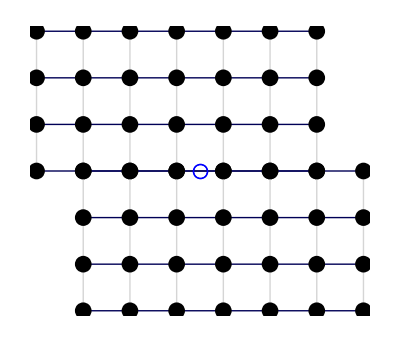
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
npoints=4;
MyPointSize=0.03;
ϕ=0;
W1=4/2;
W2=4/4;
W3=4/6;
Nq2=2;
Nq3=3;
{
{Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq2)),W2,{0,0}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq3)),W3,{0,0}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq2)),W2,{0,1/2}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq3)),W3,{0,1/2}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq2)),W2,{1/2,0}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq3)),W3,{1/2,0}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq2)),W2,{1/2,1/2}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSx[npoints,MyPointSize,2π((nq-1)/(Nq3)),W3,{1/2,1/2}],{nq,1,Nq3}]]}
}
```

marked center for reference

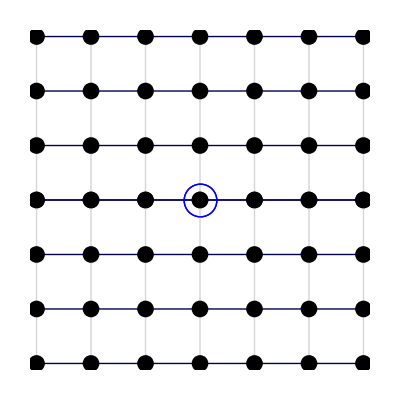
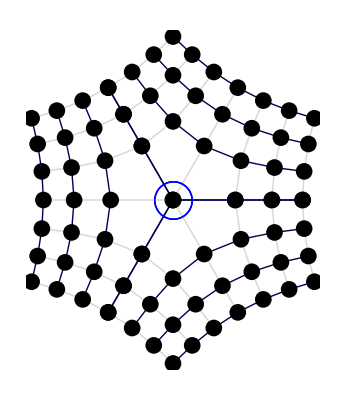
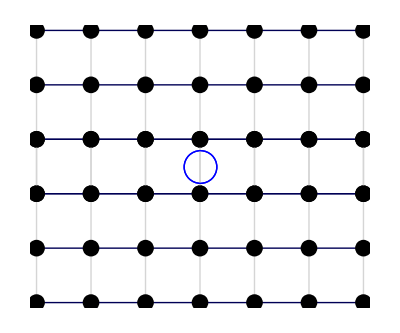
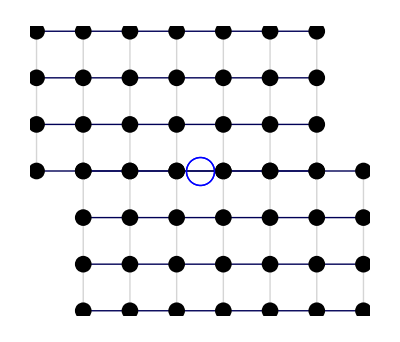
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

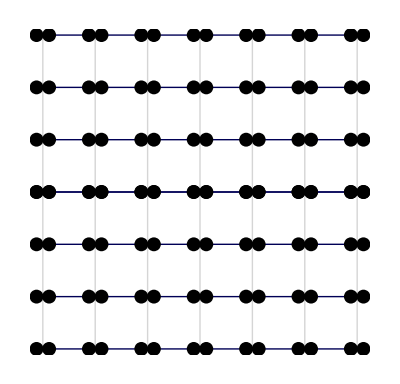
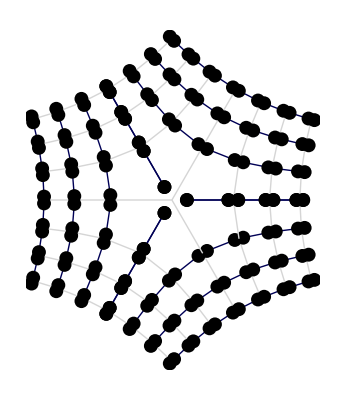
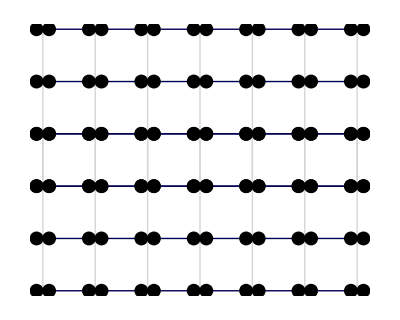
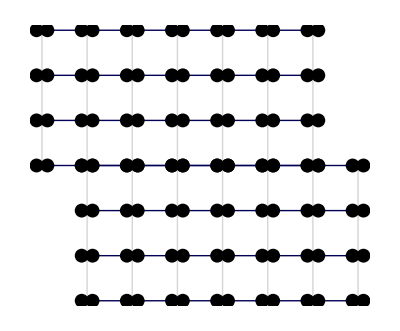
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
npoints=4;
MyPointSize=0.025;
Separation=0.12;
ϕ=0;
W1=4/2;
W2=4/4;
W3=4/6;
Nq2=2;
Nq3=3;
{
{Graphics[Table[MyFaceSxtbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq2)),W2,{0,0}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSxtbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq3)),W3,{0,0}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSxtbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq2)),W2,{0,1/2}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSxtbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq3)),W3,{0,1/2}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSxtbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq2)),W2,{1/2,0}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSxtbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq3)),W3,{1/2,0}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSxtbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq2)),W2,{1/2,1/2}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSxtbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq3)),W3,{1/2,1/2}],{nq,1,Nq3}]]}
}
```

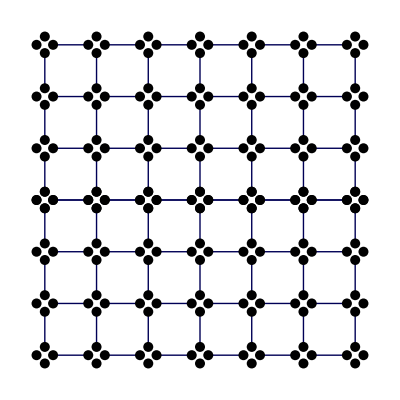
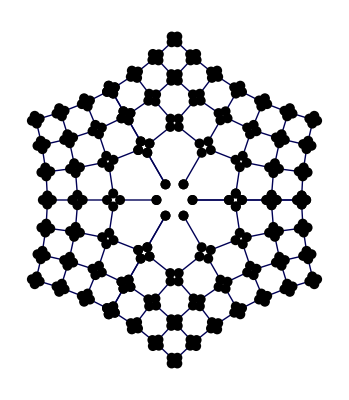
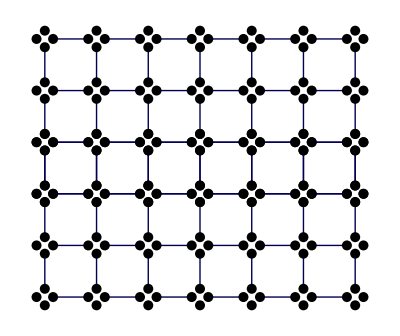
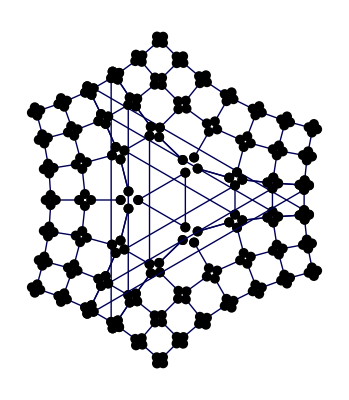
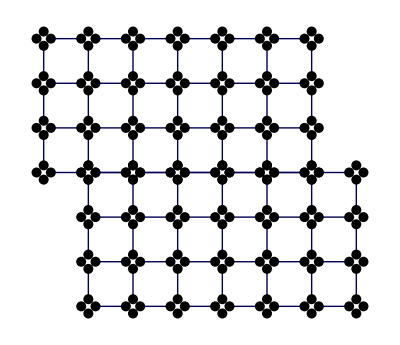
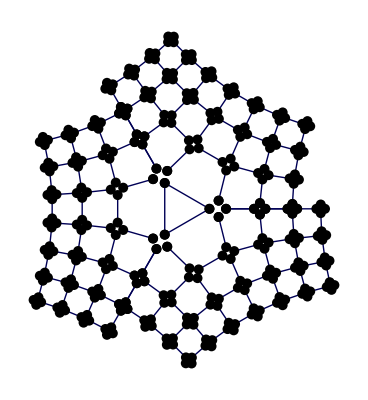
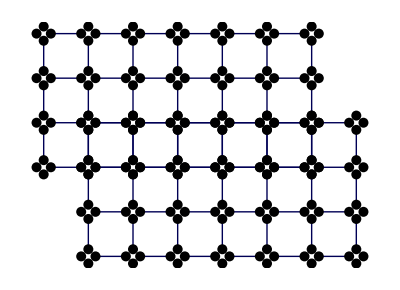
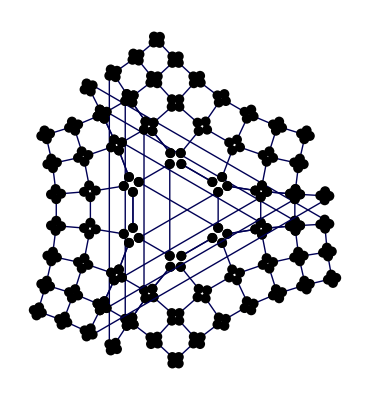

```mathematica
npoints=4;
MyPointSize=0.018;
Separation=0.16;
ϕ=0;
W1=4/2;
W2=4/4;
W3=4/6;
Nq2=2;
Nq3=3;
{
{Graphics[Table[MyFaceSxytbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq2)),W2,{0,0}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSxytbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq3)),W3,{0,0}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSxytbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq2)),W2,{0,1/2}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSxytbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq3)),W3,{0,1/2}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSxytbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq2)),W2,{1/2,0}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSxytbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq3)),W3,{1/2,0}],{nq,1,Nq3}]]},
{Graphics[Table[MyFaceSxytbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq2)),W2,{1/2,1/2}],{nq,1,Nq2}]],
Graphics[Table[MyFaceSxytbm[npoints,MyPointSize,Separation,2π((nq-1)/(Nq3)),W3,{1/2,1/2}],{nq,1,Nq3}]]}
}
```